## Pendulum swing up with angle only (observer needed) Example 7.9

```mathematica
Clear["Global`*"];
 R=1; d0=0;  q=({{1, 0}, {0, 1}}); r={{R}};polpos=1;
```

Calculate feedforward swing-up for 0 < t < τ and balance for τ < t < τ1,  based on nominal model;

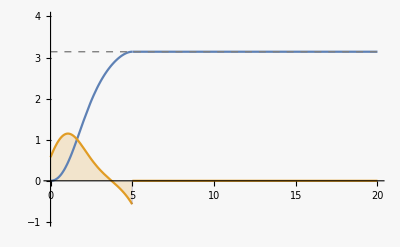

```mathematica
ffCalc[n_,τ_]:=Module[{f,θ,θdot,λ,λdot,t,Δt,bcs,eqns,sv,froot,θff0,θdotff0,uff0,θff,θdotff,uff},
Δt=τ/n;
f[{θ_,θdot_,λ_,λdot_}] := {θdot,-Sin[θ]-λ,λdot,-Cos[θ]λ};
bcs={Subscript[θ, 0]==0,Subscript[θdot, 0]==0,Subscript[θ, n]==π,Subscript[θdot, n]==0}; (* hard final constraint *)
eqns=Flatten[Join[bcs,
Table[Thread[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}== {Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}
+Δt/2(f[{Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ, i-1],Subscript[λdot, i-1]}]+f[{Subscript[θ, i],Subscript[θdot, i],Subscript[λ, i],Subscript[λdot, i]}])],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[θ, i],0},{Subscript[θdot, i],0},{Subscript[λ, i],0},{Subscript[λdot, i],0}},{i,0,n}],1];
	(* initial guesses = 0, very naive! *)
froot=FindRoot[eqns,sv];

θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ}];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ}];
uff0=ListInterpolation[Table[-Subscript[λ, i],{i,0,n}]/.froot,{0,τ}];

θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{θff,θdotff,uff}]

n=500;  τ=5;τ1=4τ;
{θ0,θdot0,u0}=ffCalc[n,τ];
p0=Plot[{θ0[t],u0[t],π},{t,0,τ1},PlotStyle->{,,Directive[Gray,Dashed,Thin]},Filling->{2->Axis},PlotRange->{-1,4}]
```

Observer & Controller gain calculations

```mathematica
{l,κ}=Module[{a,b,c,sys,poles,θ,polpos,l,κ},
a=({{0, 1}, {-Cos[θ], 0}}); b=({{0}, {1}}); c=({{1, 0}});
sys=StateSpaceModel[{a,b,c}];poles={-polpos,-polpos};
l=EstimatorGains[sys,poles] (* observer gains *);
κ=LQRegulatorGains[sys/.θ->π,{q,r}]  (* optimal feedback gains for θ=π *);
{lᵀ[[1]],κ[[1]]}]
```

{{2 polpos$1212224,polpos$1212224^2-Cos[θ$1212224]},{1/(-1+√2),1/(-1+√2)}}

Nonlinear observer

```mathematica
Observer[p_,τ1_,uff_]:=Module[{eq1,eq2,init,initError,x1,x2,xh1,xh2,xs1,xs2,xhs1,xhs2,L1,L2,t},
L1=2p;L2=p^2-Cos[xh1[t]];
initError=1;
eq1={x1'[t]==x2[t],x2'[t]==-Sin[x1[t]]+uff[t]};
eq2={xh1'[t]==xh2[t]+ L1(x1[t]-xh1[t]),xh2'[t]==-Sin[xh1[t]]+uff[t]+ L2(x1[t]-xh1[t])};
init={x1[0]==x2[0]==0,xh1[0]==xh2[0]==initError};  
{xs1,xs2,xhs1,xhs2}=NDSolveValue[{eq1, eq2,init},{x1,x2,xh1,xh2},{t,0,τ1}];
{xs1,xs2,xhs1,xhs2}]

{x1a,x2a,xh1a,xh2a}=Observer[polpos,τ1,u0];

p1a=Plot[{x1a[t],xh1a[t],π},{t,0,τ1},PlotRange->{-0.5,4.5},PlotStyle->{,,Directive[Gray,Dashed,Thin]},ImageSize->200];
p2a=Plot[{x2a[t],xh2a[t]},{t,0,τ1},PlotRange->{-1,2.2},ImageSize->200];
p3a=Plot[u0[t],{t,0,τ1},Filling->Axis,PlotRange->{-4.3,2},ImageSize->200];
(* Grid[{{p1a,p2a,p3a}},Spacings->2] *)
```

InterpolatingFunction::dmval: Input value {5.02792} lies outside the range of data in the interpolating function. Extrapolation will be used.

Nonlinear observer & linear feedback, combined

InterpolatingFunction::dmval: Input value {5.06552} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

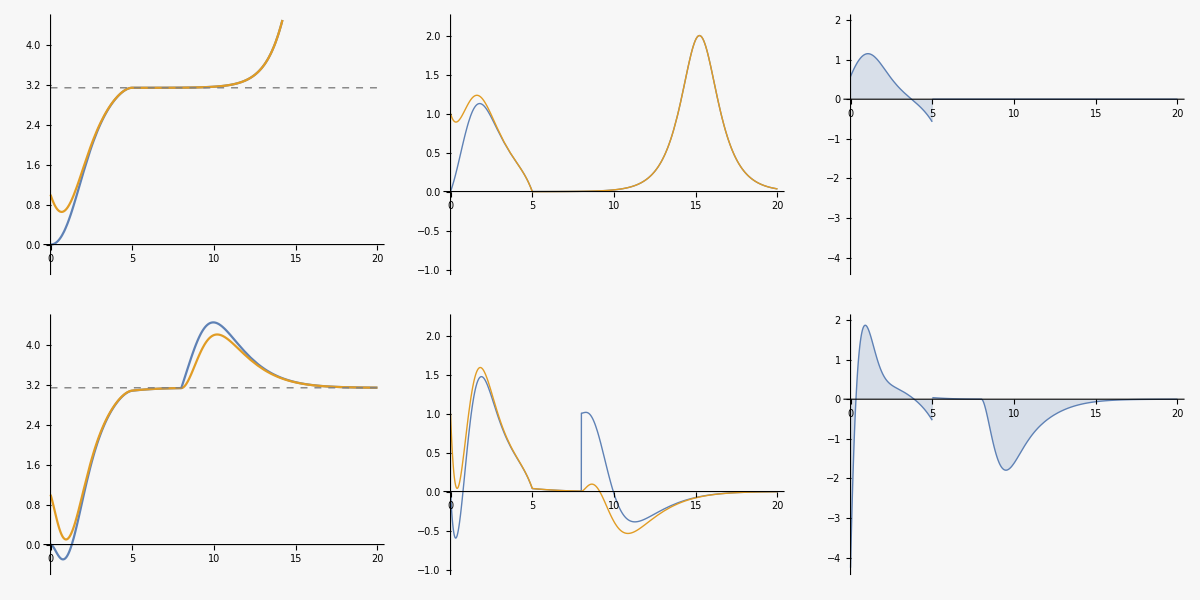

```mathematica
ObserverController[p_,κ_,τ1_,θff_,θdotff_,uff_,d_]:=Module[{eq1,eq2,init,x1,x2,xh1,xh2,xs1,xs2,xhs1,xhs2,us,ufbs,L1,L2,κ1,κ2,ufb,u,t,initError,clipval},
L1=2p;L2=p^2-Cos[xh1[t]];
κ1=κ[[1]]; κ2=κ[[2]];
initError=1;clipval=10;
ufb[t_]:=κ1(θff[t]-xh1[t])+κ2(θdotff[t]-xh2[t]); 
u=Clip[uff[t]+ufb[t],{-clipval,clipval}];
eq1={x1'[t]==x2[t],x2'[t]==-Sin[x1[t]]+u};
eq2={xh1'[t]==xh2[t]+ L1(x1[t]-xh1[t]),xh2'[t]==-Sin[xh1[t]]+u+ L2(x1[t]-xh1[t])};
init={x1[0]==x2[0]==0,xh1[0]==xh2[0]==initError};  
{xs1,xs2,xhs1,xhs2}=NDSolveValue[{eq1, eq2,init,WhenEvent[t==8,x2[t]-> x2[t]+d]},{x1,x2,xh1,xh2},{t,0,τ1}];
(* ufbs=FunctionInterpolation[κ1(θff[t]-xhs1[t])+κ2(θdotff[t]-xhs2[t]),{t,0,τ1}];*)
ufbs[t_]:=Clip[κ1(θff[t]-xhs1[t])+κ2(θdotff[t]-xhs2[t]),{-clipval,clipval}];

{xs1,xs2,xhs1,xhs2,ufbs}]

{x1b,x2b,xh1b,xh2b,uf1b}=ObserverController[polpos,κ,τ1,θ0,θdot0,u0,1];

p1b=Plot[{x1b[t],xh1b[t],π},{t,0,τ1},PlotStyle->{,,Directive[Gray,Dashed,Thin]}, PlotRange->{-0.5,4.5},ImageSize->200];
p2b=Plot[{x2b[t],xh2b[t]},{t,0,τ1},PlotRange->{-1,2.2},ImageSize->200];
p3b=Plot[u0[t]+uf1b[t],{t,0,τ1},Filling->Axis,PlotRange->{-4.3,2},ImageSize->200];
Grid[{{p1a,p2a,p3a},{p1b,p2b,p3b}},Spacings->2]
```

Top:  observer only, with bad initial conditions.  No control
Bottom:  add linear feedback control & disturbance at t = 10.

Thus, we see that the observer-controller can handle both bad initial conditions and an impulse disturbance (of force).  The undesirable spike near t=0 results from a quite inaccurate initial condition.  Limiting the control to say ±2 does not change the response significantly.

Export data

```mathematica
dt=0.05;dat=Table[Through[{x1a,x2a,xh1a,xh2a,u0,uf1b,x1b,x2b,xh1b,xh2b}[t]],{t,0,τ1,dt}]//N;
(* 
SetDirectory[NotebookDirectory[]];
Export["pendulumSwingUpObs.dat", dat];
*)
```